```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/daq-tools-bkg-auto/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadesc={Number,Number,Number,Number,Number,Number,Number,Word,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desctf_c.dat"],metadesc];
dimdesc=Dimensions[descdat][[1]];
metalvl3={Real,Real,Real,Real,Real,Real,Real,Real};
tk2[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[Table[{10^j,Superscript["10",j],{a,b}},{j,l,u,int}]~Join~Table[{10^j,"",{c,d}},{j,l+int/2,u-int/2,int}]],3];
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

ReadList::noopen: Cannot open C:\Users\tmpra\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online\desctf_c.dat.

Part::partw: Part 1 of {} does not exist.

{{2.×10^-38,8.6×10^-38,1.1×10^-29,1.×10^-10},{4.2×10^-36,1.8×10^-35,1.6×10^-19,1.×10^-10},{7.×10^-35,3.×10^-34,3.8×10^-17,1.×10^-10},{0,0,2.×10^-21,1.×10^-10},{0,0,2.×10^-21,1.×10^-10},{0,0,4.35×10^-17,1.×10^-10},{1.×10^-31,2.9×10^-26,0,1.×10^-10},{1.×10^-31,2.9×10^-26,5.4×10^-24,1.×10^-10},{1.×10^-31,2.9×10^-26,1.2×10^-16,1.×10^-10},{1.×10^-31,2.9×10^-26,1.×10^-10,0},{1.×10^-31,2.9×10^-26,1.×10^-10,0}}

All Good!

All Good 1 !

All Good 2 !

All Good 3 !

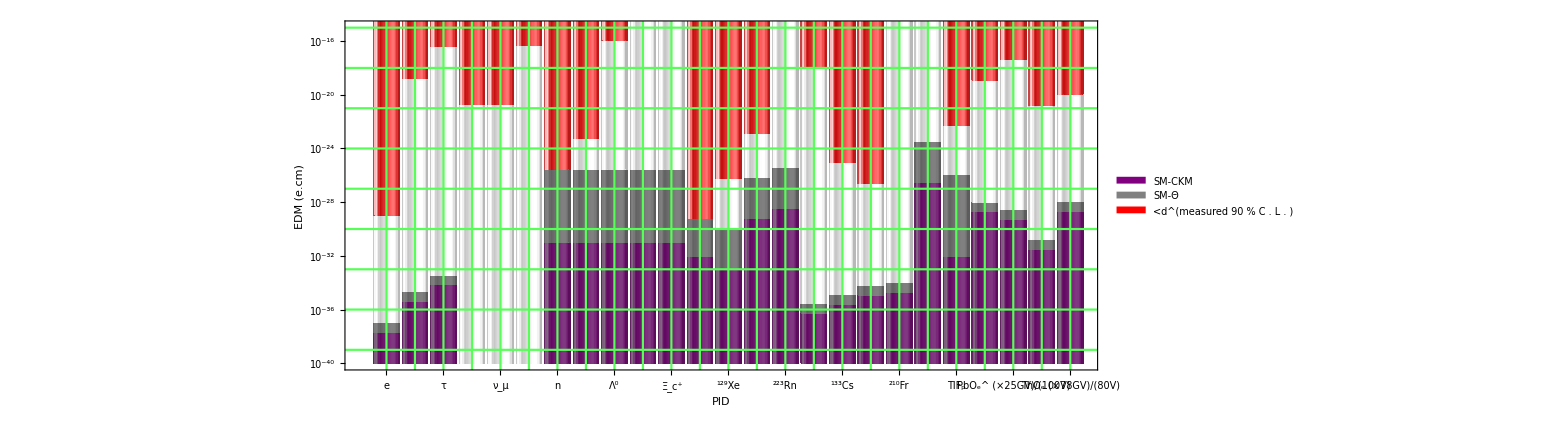

```mathematica
pttab1={
(*e*){2*N[10^(-38)],8.6*N[10^(-38)],1.1*N[10^(-29)](*New Acme paper: ACME Collaboration.Improved limit on the electric dipole moment of the electron.Nature 562,355–360 (2018)*),N[10^(-10)]},
(*mu*){4.2*N[10^(-36)],1.8*N[10^(-35)],1.6*N[10^(-19)],N[10^(-10)]},
(*τ*){7.0*N[10^(-35)],3*N[10^(-34)],3.8*N[10^(-17)],N[10^(-10)]},
(*Subscript[ν, e]*){0,0,2*N[10^(-21)],N[10^(-10)]},
(*Subscript[ν, μ]*){0,0,2*N[10^(-21)],N[10^(-10)]},
(*Subscript[ν, τ]*){0,0,4.35*N[10^(-17)],N[10^(-10)]},
(*n*){N[10^(-31)],2.9*N[10^(-26)],0,N[10^(-10)]},
(*p*){N[10^(-31)],2.9*N[10^(-26)],5.4*N[10^(-24)],N[10^(-10)]},
(*Old-Use*)
(*(*Λ^0*){1*N[10^(-32)],4.4*N[10^(-26)],1.2*N[10^(-16)],N[10^(-10)]},
(*Σ^0*){3.3*N[10^(-33)],4.4*N[10^(-26)],N[10^(-10)],0},
(*Ξ^0*){1.3*N[10^(-32)],4.4*N[10^(-26)],N[10^(-10)],0},*)
(*NEW-don't use*)
(*Λ^0*){N[10^(-31)],2.9*N[10^(-26)],1.2*N[10^(-16)],N[10^(-10)]},
(*Subscript[Λ, c]^+*){N[10^(-31)],2.9*N[10^(-26)],N[10^(-10)],0},
(*Subscript[Ξ, c]^+*){N[10^(-31)],2.9*N[10^(-26)],N[10^(-10)],0}
}
pttab2={
(*^199 Hg*){8.7*N[10^(-33)],6.2*N[10^(-30)],0,N[10^(-10)]},
(*^129 Xe*){1.2*N[10^(-33)],1.35*N[10^(-30)],5.4*N[10^(-27)],N[10^(-10)]},
(*^225 Ra*){6.3*N[10^(-30)],7.2*N[10^(-27)],1.2*N[10^(-23)],N[10^(-10)]},
(*^223 Rn*){3.2*N[10^(-29)],3.7*N[10^(-26)],N[10^(-10)],0},
(*(*^239 Pu*){3.4*N[10^(-31)],4*N[10^(-29)],N[10^(-10)],0},*)
(*^89 Rb*){5.1*N[10^(-37)],2.2*N[10^(-36)],1*N[10^(-18)],N[10^(-10)]},
(*^133 Cs*){2.3*N[10^(-36)],1.1*N[10^(-35)],9.3*N[10^(-26)],N[10^(-10)]},
(*^205 Tl*){1.2*N[10^(-35)],4.9*N[10^(-35)],2.6*N[10^(-27)],N[10^(-10)]},
(*^210 Fr*){1.8*N[10^(-35)],7.8*N[10^(-35)],N[10^(-10)],0}
};
pttab3={
(*^225 RaF^+*){6.3*N[10^(-30)]*130/.3,7.2*N[10^(-27)]*130/.3,N[10^(-10)],0},(*300kV/cm=Phys.Rev.Spec.Top. –Acc.and Beams,15,083502 (2012), 130MV/cm=Phys. Rev. A 90 052513 (2014)*)
(*TlF*){8.3*N[10^(-33)],1.2*N[10^(-26)],4.8*N[10^(-23)],N[10^(-10)]},
(*HfF^+*){2*N[10^(-29)],8.2*N[10^(-29)],1.25*N[10^(-19)],N[10^(-10)]},
(*PbO*){5*N[10^(-30)],2.2*N[10^(-29)],4.3*N[10^(-18)],N[10^(-10)]},
(*YbF*){2.9*N[10^(-32)],1.25*N[10^(-31)],1.54*N[10^(-21)],N[10^(-10)]},
(*ThO*){4.3*36/80*N[10^(-29)],1.86*36/80*N[10^(-28)],2*36/80*1.1/8.7*N[10^(-19)],N[10^(-10)]}(*36/80 comes from new Electric field used in Nature-Acme paper*)
};
pttab=Join[pttab1,pttab2,pttab3];
particles1={"e","μ","τ","ν_e","ν_μ","ν_τ","n","p","Λ^0",(*"Σ^0","Ξ^0"*)"Λ_c^+","Ξ_c^+"};
particles2={"^199Hg","^129Xe","^225Ra","^223Rn",(*"^239Pu",*)"^89Rb","^133Cs","^205Tl","^210Fr"};
particles3={"RaF_n^+
(×130MV)/(300kV)","TlF_p","HfF_e^+
(×23GV)/(24V)","PbO_e^
(×25GV)/(100V)","YbF_e
(×14.5GV)/(10kV)","ThO_e
(×78GV)/(80V)"};
particles=Join[particles1,particles2,particles3];
(**Formatting**)
thk=.002;
If[Dimensions[pttab][[1]]==Dimensions[particles][[1]],Print["All Good!"],Print["Re-check data and names!"]];
If[Dimensions[pttab1][[1]]==Dimensions[particles1][[1]],Print["All Good 1 !"],Print["Re-check data and names!"]];
If[Dimensions[pttab2][[1]]==Dimensions[particles2][[1]],Print["All Good 2 !"],Print["Re-check data and names!"]];
If[Dimensions[pttab3][[1]]==Dimensions[particles3][[1]],Print["All Good 3 !"],Print["Re-check data and names!"]];
numpart=Dimensions[particles][[1]];
numpart1=Dimensions[particles1][[1]];
numpart2=Dimensions[particles2][[1]];
numpart3=Dimensions[particles3][[1]];
ptsty=-39;pteny=-9;ptinty=3;
gridln={Table[k,{k,1,numpart,1}],Table[N[10^(k)],{k,ptsty,pteny,ptinty}]};
gridln1={Table[k,{k,1,numpart1,1}],Table[N[10^(k)],{k,ptsty,pteny,ptinty}]};
gridln2={Table[k,{k,1,numpart2,1}],Table[N[10^(k)],{k,ptsty,pteny,ptinty}]};
gridln3={Table[k,{k,1,numpart3,1}],Table[N[10^(k)],{k,ptsty,pteny,ptinty}]};
tks={(*y,x*){tk2[ptsty,pteny,.015,0,0,0,ptinty],tk2[ptsty,pteny,.015,0,0,0,ptinty]},{Table[{k,particles[[k]],{0.015,0}},{k,1,numpart}],None}};
tks1={(*y,x*){tk2[ptsty,pteny,.015,0,0,0,ptinty],tk2[ptsty,pteny,.015,0,0,0,ptinty]},{Table[{k,particles1[[k]],{0.015,0}},{k,1,numpart1}],None}};
tks2={(*y,x*){tk2[ptsty,pteny,.015,0,0,0,ptinty],tk2[ptsty,pteny,.015,0,0,0,ptinty]},{Table[{k,particles2[[k]],{0.015,0}},{k,1,numpart2}],None}};tks3={(*y,x*){tk2[ptsty,pteny,.015,0,0,0,ptinty],tk2[ptsty,pteny,.015,0,0,0,ptinty]},{Table[{k,particles3[[k]],{0.015,0}},{k,1,numpart3}],None}};
cht=BarChart[pttab,PlotRange->{Automatic,{N[10^(-40)],N[10^(-15)]}},(*GridLines->gridln,*)ChartLayout->"Stacked",ScalingFunctions->"Log",ChartLegends->Placed[{"SM-CKM","SM-Θ","","<d^(measured  90  % C . L . )"},Top],Frame->True,FrameStyle->Thickness[thk],FrameTicksStyle->{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]},FrameLabel->{"PID","EDM (e.cm)"},LabelStyle->{26,Black,Bold},TicksStyle->{Directive[FontSize->26]},
FrameTicks->tks,ChartStyle->{Purple,Gray,White,Red},GridLines->gridln,GridLinesStyle->Directive[Lighter[Green],Thickness[thk/2]],ChartBaseStyle->EdgeForm[None],ChartElementFunction->"GlassRectangle",AspectRatio->.28,ImageSize->2200]
```

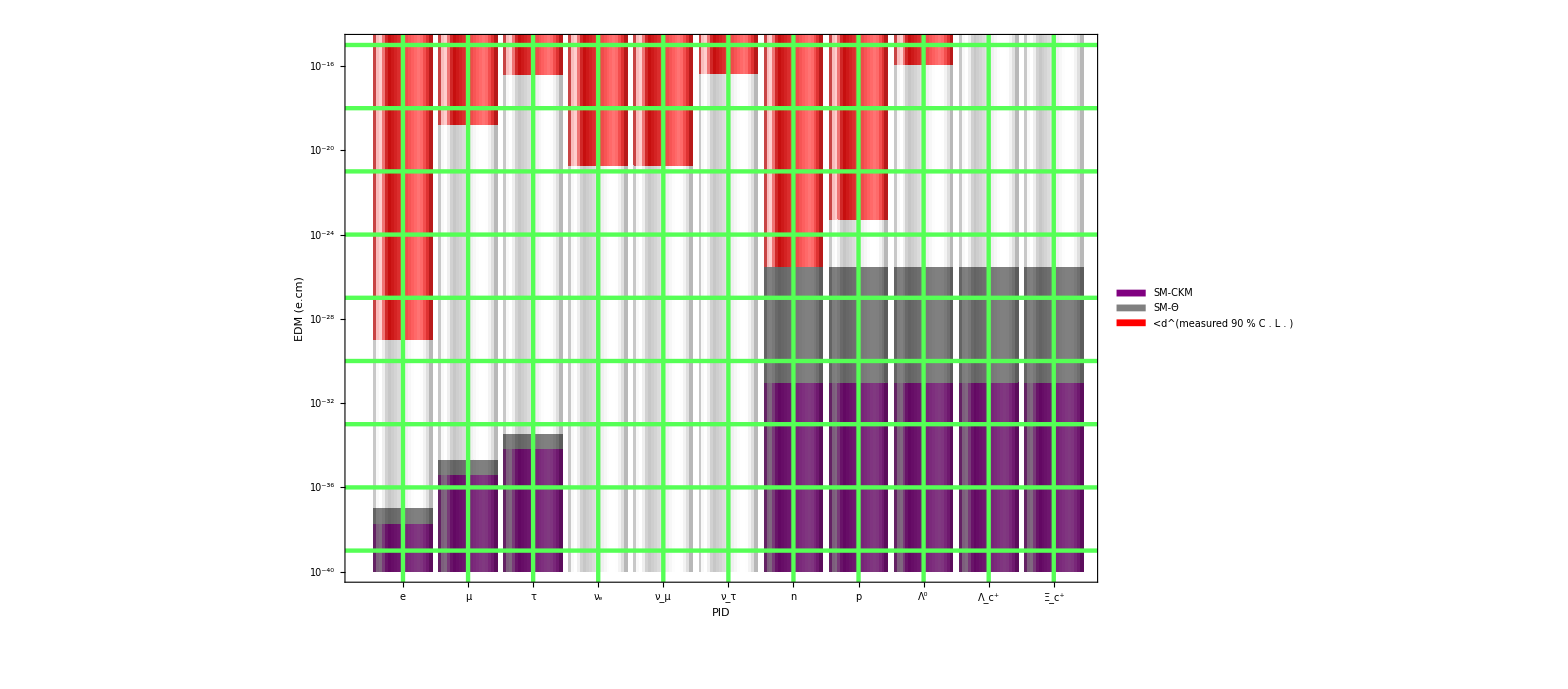

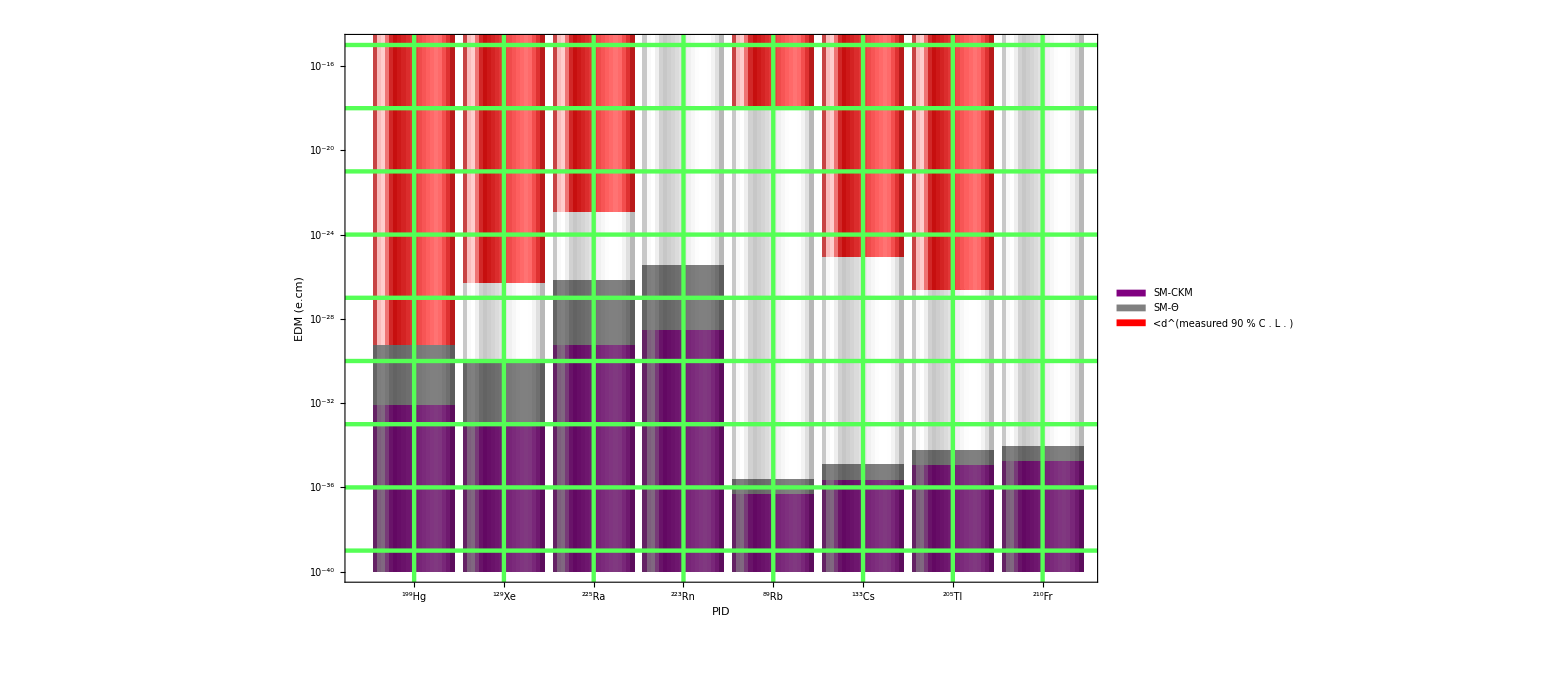

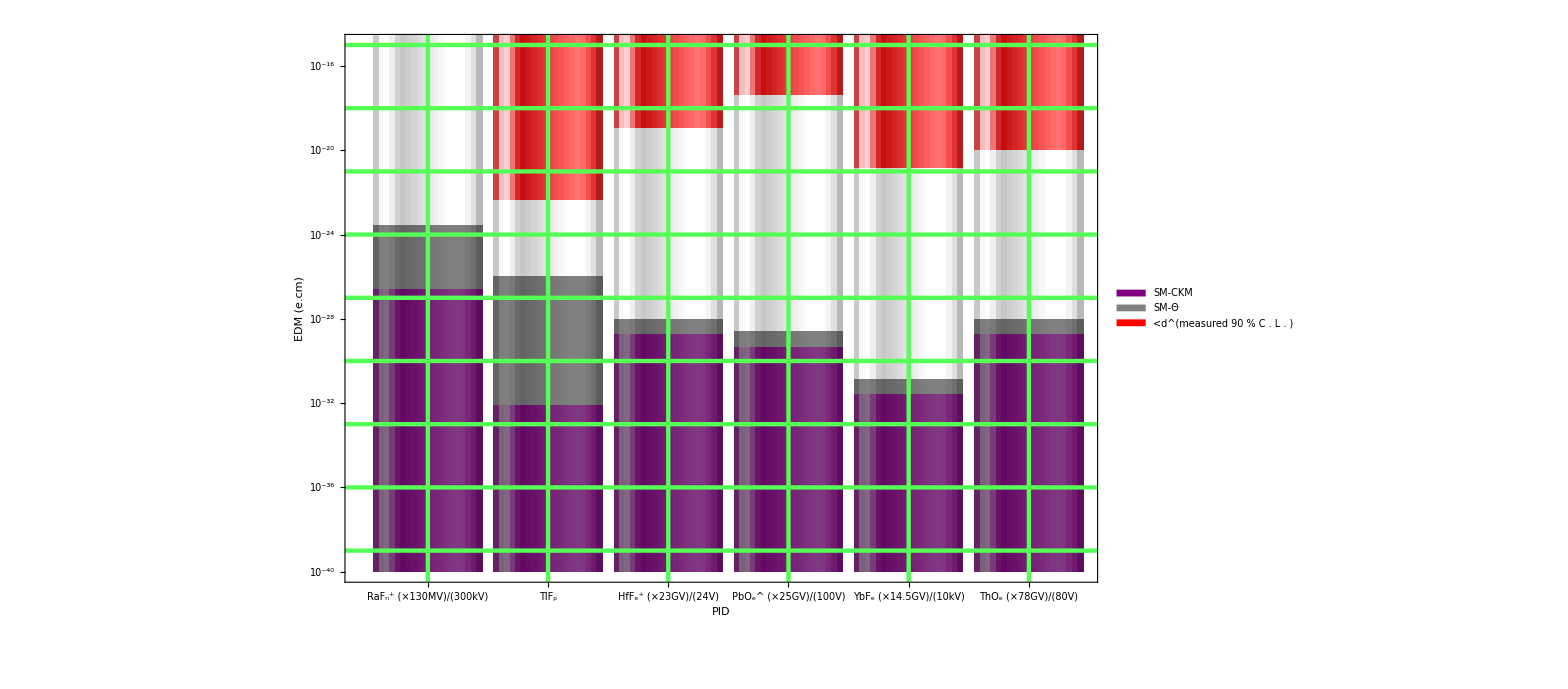

```mathematica
thk=.004;
cht1=BarChart[pttab1,PlotRange->{Automatic,{N[10^(-40)],N[10^(-15)]}},(*GridLines->gridln,*)ChartLayout->"Stacked",ScalingFunctions->"Log",ChartLegends->Placed[{"SM-CKM","SM-Θ","","<d^(measured  90  % C . L . )"},Top],Frame->True,FrameStyle->Thickness[thk],FrameTicksStyle->{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]},FrameLabel->{"PID","EDM (e.cm)"},LabelStyle->{32,Black,Bold},TicksStyle->{Directive[FontSize->32]},
FrameTicks->tks1,ChartStyle->{Purple,Gray,White,Red},GridLines->gridln,GridLinesStyle->Directive[Lighter[Green],Thickness[thk/2]],ChartBaseStyle->EdgeForm[None],ChartElementFunction->"GlassRectangle",AspectRatio->(numpart1/numpart),ImageSize->3600*(numpart1/numpart)]
cht2=BarChart[pttab2,PlotRange->{Automatic,{N[10^(-40)],N[10^(-15)]}},(*GridLines->gridln,*)ChartLayout->"Stacked",ScalingFunctions->"Log",ChartLegends->Placed[{"SM-CKM","SM-Θ","","<d^(measured  90  % C . L . )"},Top],Frame->True,FrameStyle->Thickness[thk],FrameTicksStyle->{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]},FrameLabel->{"PID","EDM (e.cm)"},LabelStyle->{32,Black,Bold},TicksStyle->{Directive[FontSize->32]},
FrameTicks->tks2,ChartStyle->{Purple,Gray,White,Red},GridLines->gridln,GridLinesStyle->Directive[Lighter[Green],Thickness[thk/2]],ChartBaseStyle->EdgeForm[None],ChartElementFunction->"GlassRectangle",AspectRatio->(numpart1/numpart),ImageSize->3600*(numpart1/numpart)]
cht3=BarChart[pttab3,PlotRange->{Automatic,{N[10^(-40)],N[10^(-15)]}},(*GridLines->gridln,*)ChartLayout->"Stacked",ScalingFunctions->"Log",ChartLegends->Placed[{"SM-CKM","SM-Θ","","<d^(measured  90  % C . L . )"},Top],Frame->True,FrameStyle->Thickness[thk],FrameTicksStyle->{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]},FrameLabel->{"PID","EDM (e.cm)"},LabelStyle->{32,Black,Bold},TicksStyle->{Directive[FontSize->32]},
FrameTicks->tks3,ChartStyle->{Purple,Gray,White,Red},GridLines->gridln,GridLinesStyle->Directive[Lighter[Green],Thickness[thk/2]],ChartBaseStyle->EdgeForm[None],ChartElementFunction->"GlassRectangle",AspectRatio->(numpart1/numpart),ImageSize->3600*(numpart1/numpart)]
```

```mathematica
Export[StringJoin[PicDir,seperator,"EDM_all.png"],cht]
Export[StringJoin[PicDir,seperator,"EDM_fp.png"],cht1]
Export[StringJoin[PicDir,seperator,"EDM_atom.png"],cht2]
Export[StringJoin[PicDir,seperator,"EDM_mol.png"],cht2]
```

C:\Users\tmpra\Dropbox\nEDM\Pictures\EDM_all.png

C:\Users\tmpra\Dropbox\nEDM\Pictures\EDM_fp.png

C:\Users\tmpra\Dropbox\nEDM\Pictures\EDM_atom.png

C:\Users\tmpra\Dropbox\nEDM\Pictures\EDM_mol.png